## Parton Level Cross Section

The parton - level cross section can be evaluated by using two Fourier Transforms :

### -Graphics-

```mathematica
F1[x_,y_]=FourierTransform[1/(lx^2+ly^2),{lx,ly},{x,y}]
```

1/2 (-HeavisideTheta[-x] (2 EulerGamma+2 Log[-x]+Log[1+y^2/x^2])-HeavisideTheta[x] (2 EulerGamma+2 Log[x]+Log[1+y^2/x^2]))

It only depends on r=√(x^2+y^2) as it should.

```mathematica
F1[r_]=-1/(2π)Log[r]
F1[{x_,y_}]=-1/π Log[x^2+y^2]
```

-Log[r]/(2 π)

-Log[x^2+y^2]/π

```mathematica
Ω[d_]:=(2 π^(d/2))/Gamma[d/2]
```

```mathematica
setd:={d->2+2ϵ}
```

```mathematica
F1[r_,ϵ_]=F1DR=1/2 μ^(2-d)Ω[d-1]/(2π)^(d-1) r^(-(d-2))Gamma[d-2]/.setd//FullSimplify
```

1/4 π^(-1-ϵ) r^(-2 ϵ) μ^(-2 ϵ) Gamma[ϵ]

```mathematica
F1[{x_,y_},ϵ_]=1/4 π^(-1-ϵ) Sqrt[x^2+y^2]^(-2 ϵ) μ^(-2 ϵ) Gamma[ϵ]
```

1/4 π^(-1-ϵ) (x^2+y^2)^-ϵ μ^(-2 ϵ) Gamma[ϵ]

### -Graphics-

We would like to evalue the Fourier Transform of (k<->l compared to the note)

```mathematica
itg:=1/(lx^2+ly^2)(lx (lx-kx) + ly (ly-ky))/((lx-kx)^2+(ly-ky)^2)
```

Then it is trivial to integrate out lx first. We close the integration contour upward in the complex plane:

```mathematica
intkxana[ly_,{kx_,ky_}]=(FullSimplify[I HeavisideTheta[ly]Residue[itg,{lx,I ly}]]+FullSimplify[I HeavisideTheta[-ly]Residue[itg,{lx,-I ly}]]+FullSimplify[I HeavisideTheta[ly-ky]Residue[itg,{lx,kx+I (ly-ky)}]]+FullSimplify[I HeavisideTheta[-ly+ky]Residue[itg,{lx,kx-I (ly-ky)}]])
```

HeavisideTheta[ky-ly]/(2 (-ⅈ kx+ky-2 ly))+HeavisideTheta[-ly]/(2 (ⅈ kx+ky-2 ly))+HeavisideTheta[ly]/(2 (ⅈ kx-ky+2 ly))-HeavisideTheta[-ky+ly]/(2 (ⅈ kx+ky-2 ly))

```mathematica
intkxnum[ly_,{kx_,ky_}]:=1/(2π)NIntegrate[1/(lx^2+ly^2)(lx (lx-kx) + ly (ly-ky))/((lx-kx)^2+(ly-ky)^2),{lx,-Infinity,Infinity}]
```

```mathematica
ftkx:=(ⅈ HeavisideTheta[ky-ly])/(2 (kx+ⅈ ky-2 ⅈ ly))-(ⅈ HeavisideTheta[-ly])/(2 (kx-ⅈ ky+2 ⅈ ly))-(ⅈ HeavisideTheta[ly])/(2 (kx+ⅈ ky-2 ⅈ ly))+(ⅈ HeavisideTheta[-ky+ly])/(2 (kx-ⅈ ky+2 ⅈ ly))
```

```mathematica
cond:=r>0&&x∈Reals&&y∈Reals&&2 π>ϕ>0 &&ly∈Reals&&kx∈Reals&&ky∈Reals
```

```mathematica
intkxana[-1.0,{-0.3,-0.1}]
intkxnum[-1.0,{-0.3,-0.1}]
```

0.513514+0. ⅈ

0.513514

```mathematica
FplusFF[y_,a_]=Assuming[cond,FourierTransform[1/(√(2π))HeavisideTheta[l]/(l-a),l,y]//FullSimplify]
FminusFF[y_,a_]=Assuming[cond,FourierTransform[1/(√(2π))HeavisideTheta[-l]/(l-a),l,y]//FullSimplify]
```

(ⅇ^(ⅈ a y) (ⅈ π y+Abs[y] (-2 CosIntegral[-a y]+Log[1/y^2]+2 Log[y]+2 ⅈ SinIntegral[a y])))/(4 π Abs[y])

(ⅇ^(ⅈ a y) (ⅈ π y+Abs[y] (2 CosIntegral[a y]-2 Log[y]+Log[y^2]-2 ⅈ SinIntegral[a y])))/(4 π Abs[y])

```mathematica
Ce[y_]=-CosIntegral[y]-I SinIntegral[y]+I Integrate[Sin[t]/t,{t,0,Infinity}]
Fplus[y_,a_]=Exp[-I a y]/(2π)(Ce[a y]-2π I HeavisideTheta[Im[a]] HeavisideTheta[-y])
Fminus[y_,a_]=-Exp[-I a y]/(2π)(Ce[a y]-2π I HeavisideTheta[-Im[a]] HeavisideTheta[y])
```

(ⅈ π)/2-CosIntegral[y]-ⅈ SinIntegral[y]

(ⅇ^(-ⅈ a y) ((ⅈ π)/2-CosIntegral[a y]-2 ⅈ π HeavisideTheta[-y] HeavisideTheta[Im[a]]-ⅈ SinIntegral[a y]))/(2 π)

-(ⅇ^(-ⅈ a y) ((ⅈ π)/2-CosIntegral[a y]-2 ⅈ π HeavisideTheta[y] HeavisideTheta[-Im[a]]-ⅈ SinIntegral[a y]))/(2 π)

```mathematica
F3[r_,{kx_,ky_}]=Assuming[cond,1/(√(2π))FourierTransform[intkxana[ly,{kx,ky}],ly,r]//FullSimplify]
```

1/(8 π)ⅇ^(-1/2 (kx-ⅈ ky) r) (-CosIntegral[1/2 (-ⅈ kx+ky) r]-CosIntegral[1/2 (ⅈ kx+ky) r]-SinhIntegral[1/2 (kx-ⅈ ky) r]-SinhIntegral[1/2 (kx+ⅈ ky) r]-ⅇ^(kx r) (CosIntegral[-1/2 ⅈ (kx-ⅈ ky) r]+CosIntegral[1/2 ⅈ (kx+ⅈ ky) r]-SinhIntegral[1/2 (kx+ⅈ ky) r]+ⅈ SinIntegral[1/2 (ⅈ kx+ky) r]))

```mathematica
aa={kx,ky}-Total[{x,y}.{kx,ky}]{x,y}/r^2
```

{kx-(x (kx x+ky y))/r^2,ky-(y (kx x+ky y))/r^2}

```mathematica
F3[{x_,y_},{kx_,ky_}]=Module[{r,k1u,k1,k2},
r=Sqrt[x^2+y^2];
k1u={kx,ky}-Total[{x,y}.{kx,ky}]{x,y}/r^2;
k1=Sqrt[Total[k1u.k1u]];
k2=Total[{x,y}.{kx,ky}]/r;
F3[r,{k1,k2}]//FullSimplify
]
```

-1/(8 π)ⅇ^(1/2 (ⅈ kx x+ⅈ ky y-√((ky x-kx y)^2/(x^2+y^2)) √(x^2+y^2))) (CosIntegral[1/2 (kx x+ky y-ⅈ √((ky x-kx y)^2/(x^2+y^2)) √(x^2+y^2))]+CosIntegral[1/2 (kx x+ky y+ⅈ √((ky x-kx y)^2/(x^2+y^2)) √(x^2+y^2))]-SinhIntegral[1/2 (ⅈ kx x+ⅈ ky y-√((ky x-kx y)^2/(x^2+y^2)) √(x^2+y^2))]+SinhIntegral[1/2 (ⅈ kx x+ⅈ ky y+√((ky x-kx y)^2/(x^2+y^2)) √(x^2+y^2))]+ⅇ^(√((ky x-kx y)^2/(x^2+y^2)) √(x^2+y^2)) (CosIntegral[1/2 (-kx x-ky y-ⅈ √((ky x-kx y)^2/(x^2+y^2)) √(x^2+y^2))]+CosIntegral[1/2 ⅈ (ⅈ kx x+ⅈ ky y+√((ky x-kx y)^2/(x^2+y^2)) √(x^2+y^2))]-SinhIntegral[1/2 (ⅈ kx x+ⅈ ky y+√((ky x-kx y)^2/(x^2+y^2)) √(x^2+y^2))]+ⅈ SinIntegral[1/2 (kx x+ky y+ⅈ √((ky x-kx y)^2/(x^2+y^2)) √(x^2+y^2))]))

```mathematica
Assuming[x^2+y^2>0,FullSimplify[-1/(8 π)ⅇ^(1/2 (ⅈ kx x+ⅈ ky y-√((ky x-kx y)^2/(x^2+y^2)) √(x^2+y^2))) (CosIntegral[1/2 (kx x+ky y-ⅈ √((ky x-kx y)^2/(x^2+y^2)) √(x^2+y^2))]+CosIntegral[1/2 (kx x+ky y+ⅈ √((ky x-kx y)^2/(x^2+y^2)) √(x^2+y^2))]-SinhIntegral[1/2 (ⅈ kx x+ⅈ ky y-√((ky x-kx y)^2/(x^2+y^2)) √(x^2+y^2))]+SinhIntegral[1/2 (ⅈ kx x+ⅈ ky y+√((ky x-kx y)^2/(x^2+y^2)) √(x^2+y^2))]+ⅇ^(√((ky x-kx y)^2/(x^2+y^2)) √(x^2+y^2)) (CosIntegral[1/2 (-kx x-ky y-ⅈ √((ky x-kx y)^2/(x^2+y^2)) √(x^2+y^2))]+CosIntegral[1/2 ⅈ (ⅈ kx x+ⅈ ky y+√((ky x-kx y)^2/(x^2+y^2)) √(x^2+y^2))]-SinhIntegral[1/2 (ⅈ kx x+ⅈ ky y+√((ky x-kx y)^2/(x^2+y^2)) √(x^2+y^2))]+ⅈ SinIntegral[1/2 (kx x+ky y+ⅈ √((ky x-kx y)^2/(x^2+y^2)) √(x^2+y^2))]))]]
```

-1/(8 π)ⅇ^(1/2 (ⅈ kx x+ⅈ ky y-√((ky x-kx y)^2))) (CosIntegral[1/2 (kx x+ky y-ⅈ √((ky x-kx y)^2))]+CosIntegral[1/2 (kx x+ky y+ⅈ √((ky x-kx y)^2))]-SinhIntegral[1/2 (ⅈ kx x+ⅈ ky y-√((ky x-kx y)^2))]+SinhIntegral[1/2 (ⅈ kx x+ⅈ ky y+√((ky x-kx y)^2))]+ⅇ^(√((ky x-kx y)^2)) (CosIntegral[1/2 (-kx x-ky y-ⅈ √((ky x-kx y)^2))]+CosIntegral[1/2 ⅈ (ⅈ kx x+ⅈ ky y+√((ky x-kx y)^2))]-SinhIntegral[1/2 (ⅈ kx x+ⅈ ky y+√((ky x-kx y)^2))]+ⅈ SinIntegral[1/2 (kx x+ky y+ⅈ √((ky x-kx y)^2))]))

```mathematica
F3num[{x_,y_},{kx_,ky_}]:=1/(2π)^2 NIntegrate[1/(lx^2+ly^2)(lx (lx-kx) + ly (ly-ky))/((lx-kx)^2+(ly-ky)^2)Exp[I (lx x +ly y)],{lx,-Infinity,Infinity},{ly,-Infinity,Infinity}]
```

```mathematica
{F3[r,{kx,ky}],F3num[{0,r},{kx,ky}]}/.{r->1,kx->0.5,ky->0.5}
{F3[r,{kx,ky}],F3num[{0,r},{kx,ky}]}/.{r->1,kx->0.5,ky->-0.5}
{F3[r,{kx,ky}],F3num[{0,r},{kx,ky}]}/.{r->1,kx->-0.5,ky->0.5}
{F3[r,{kx,ky}],F3num[{0,r},{kx,ky}]}/.{r->1,kx->-0.5,ky->-0.5}
```

NIntegrate::inumr: The integrand (ⅇ^(ⅈ ly r) (lx (-kx+lx)+ly (-ky+ly)))/((lx^2+ly^2) ((-kx+lx)^2+(-ky+ly)^2)) has evaluated to non-numerical values for all sampling points in the region with boundaries {{-∞,0.},{-∞,0.}}.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in ly near {lx,ly} = {356929.,2318.86}. NIntegrate obtained 3.28731+0.839062 ⅈ and 0.0172553 for the integral and error estimates.

{0.0832587+0.0212594 ⅈ,0.0832686+0.0212537 ⅈ}

NIntegrate::inumr: The integrand (ⅇ^(ⅈ ly r) (lx (-kx+lx)+ly (-ky+ly)))/((lx^2+ly^2) ((-kx+lx)^2+(-ky+ly)^2)) has evaluated to non-numerical values for all sampling points in the region with boundaries {{-∞,0.},{-∞,0.}}.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in ly near {lx,ly} = {356929.,-2318.86}. NIntegrate obtained 3.28731-0.839062 ⅈ and 0.0172553 for the integral and error estimates.

{0.0832587-0.0212594 ⅈ,0.0832686-0.0212537 ⅈ}

NIntegrate::inumr: The integrand (ⅇ^(ⅈ ly r) (lx (-kx+lx)+ly (-ky+ly)))/((lx^2+ly^2) ((-kx+lx)^2+(-ky+ly)^2)) has evaluated to non-numerical values for all sampling points in the region with boundaries {{-∞,0.},{-∞,0.}}.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in ly near {lx,ly} = {-356929.,2318.86}. NIntegrate obtained 3.28731+0.839062 ⅈ and 0.0172553 for the integral and error estimates.

{0.0832587+0.0212594 ⅈ,0.0832686+0.0212537 ⅈ}

NIntegrate::inumr: The integrand (ⅇ^(ⅈ ly r) (lx (-kx+lx)+ly (-ky+ly)))/((lx^2+ly^2) ((-kx+lx)^2+(-ky+ly)^2)) has evaluated to non-numerical values for all sampling points in the region with boundaries {{-∞,0.},{-∞,0.}}.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in ly near {lx,ly} = {-356929.,-2318.86}. NIntegrate obtained 3.28731-0.839062 ⅈ and 0.0172553 for the integral and error estimates.

{0.0832587-0.0212594 ⅈ,0.0832686-0.0212537 ⅈ}

```mathematica
{F3[r,{kx,ky}],F3num[{0,r},{kx,ky}]}/.{r->-1,kx->0.5,ky->0.5}
{F3[r,{kx,ky}],F3num[{0,r},{kx,ky}]}/.{r->-1,kx->0.5,ky->-0.5}
{F3[r,{kx,ky}],F3num[{0,r},{kx,ky}]}/.{r->-1,kx->-0.5,ky->0.5}
{F3[r,{kx,ky}],F3num[{0,r},{kx,ky}]}/.{r->-1,kx->-0.5,ky->-0.5}
```

NIntegrate::inumr: The integrand (ⅇ^(ⅈ ly r) (lx (-kx+lx)+ly (-ky+ly)))/((lx^2+ly^2) ((-kx+lx)^2+(-ky+ly)^2)) has evaluated to non-numerical values for all sampling points in the region with boundaries {{-∞,0.},{-∞,0.}}.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in ly near {lx,ly} = {356929.,2318.86}. NIntegrate obtained 3.28731-0.839062 ⅈ and 0.0172553 for the integral and error estimates.

{0.0832587-0.0212594 ⅈ,0.0832686-0.0212537 ⅈ}

NIntegrate::inumr: The integrand (ⅇ^(ⅈ ly r) (lx (-kx+lx)+ly (-ky+ly)))/((lx^2+ly^2) ((-kx+lx)^2+(-ky+ly)^2)) has evaluated to non-numerical values for all sampling points in the region with boundaries {{-∞,0.},{-∞,0.}}.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in ly near {lx,ly} = {356929.,-2318.86}. NIntegrate obtained 3.28731+0.839062 ⅈ and 0.0172553 for the integral and error estimates.

{0.0832587+0.0212594 ⅈ,0.0832686+0.0212537 ⅈ}

NIntegrate::inumr: The integrand (ⅇ^(ⅈ ly r) (lx (-kx+lx)+ly (-ky+ly)))/((lx^2+ly^2) ((-kx+lx)^2+(-ky+ly)^2)) has evaluated to non-numerical values for all sampling points in the region with boundaries {{-∞,0.},{-∞,0.}}.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in ly near {lx,ly} = {-356929.,2318.86}. NIntegrate obtained 3.28731-0.839062 ⅈ and 0.0172553 for the integral and error estimates.

{0.0832587-0.0212594 ⅈ,0.0832686-0.0212537 ⅈ}

NIntegrate::inumr: The integrand (ⅇ^(ⅈ ly r) (lx (-kx+lx)+ly (-ky+ly)))/((lx^2+ly^2) ((-kx+lx)^2+(-ky+ly)^2)) has evaluated to non-numerical values for all sampling points in the region with boundaries {{-∞,0.},{-∞,0.}}.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in ly near {lx,ly} = {-356929.,-2318.86}. NIntegrate obtained 3.28731+0.839062 ⅈ and 0.0172553 for the integral and error estimates.

{0.0832587+0.0212594 ⅈ,0.0832686+0.0212537 ⅈ}

```mathematica
({{x,y},{kx,ky},F3[{x,y},{kx,ky}],F3num[{x,y},{kx,ky}]})/.{x->-1.5,y->1.0,kx->0.5,ky->0.5}
({{x,y},{kx,ky},F3[{x,y},{kx,ky}],F3num[{x,y},{kx,ky}]})/.{x->-1.5,y->-1.0,kx->0.5,ky->0.5}
({{x,y},{kx,ky},F3[{x,y},{kx,ky}],F3num[{x,y},{kx,ky}]})/.{x->1.5,y->-1.0,kx->0.5,ky->0.5}
({{x,y},{kx,ky},F3[{x,y},{kx,ky}],F3num[{x,y},{kx,ky}]})/.{x->1.5,y->1.0,kx->0.5,ky->0.5}
```

NIntegrate::inumr: The integrand (ⅇ^(ⅈ (lx x+ly y)) (lx (-kx+lx)+ly (-ky+ly)))/((lx^2+ly^2) ((-kx+lx)^2+(-ky+ly)^2)) has evaluated to non-numerical values for all sampling points in the region with boundaries {{-∞,0.},{-∞,0.}}.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in lx near {lx,ly} = {0.499998,0.499998}. NIntegrate obtained 0.985257-0.123802 ⅈ and 0.000411768 for the integral and error estimates.

{{-1.5,1.},{0.5,0.5},0.0249569-0.00313596 ⅈ,0.0249568-0.00313595 ⅈ}

NIntegrate::inumr: The integrand (ⅇ^(ⅈ (lx x+ly y)) (lx (-kx+lx)+ly (-ky+ly)))/((lx^2+ly^2) ((-kx+lx)^2+(-ky+ly)^2)) has evaluated to non-numerical values for all sampling points in the region with boundaries {{-∞,0.},{-∞,0.}}.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in lx near {lx,ly} = {0.499998,0.499998}. NIntegrate obtained -0.101235+0.0730444 ⅈ and 0.000420419 for the integral and error estimates.

{{-1.5,-1.},{0.5,0.5},-0.00256429+0.00185009 ⅈ,-0.0025643+0.00185024 ⅈ}

NIntegrate::inumr: The integrand (ⅇ^(ⅈ (lx x+ly y)) (lx (-kx+lx)+ly (-ky+ly)))/((lx^2+ly^2) ((-kx+lx)^2+(-ky+ly)^2)) has evaluated to non-numerical values for all sampling points in the region with boundaries {{-∞,0.},{-∞,0.}}.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in lx near {lx,ly} = {0.499998,0.499998}. NIntegrate obtained 0.985257+0.123802 ⅈ and 0.000411768 for the integral and error estimates.

{{1.5,-1.},{0.5,0.5},0.0249569+0.00313596 ⅈ,0.0249568+0.00313595 ⅈ}

NIntegrate::inumr: The integrand (ⅇ^(ⅈ (lx x+ly y)) (lx (-kx+lx)+ly (-ky+ly)))/((lx^2+ly^2) ((-kx+lx)^2+(-ky+ly)^2)) has evaluated to non-numerical values for all sampling points in the region with boundaries {{-∞,0.},{-∞,0.}}.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in lx near {lx,ly} = {0.499998,0.499998}. NIntegrate obtained -0.101235-0.0730444 ⅈ and 0.000420419 for the integral and error estimates.

{{1.5,1.},{0.5,0.5},-0.00256429-0.00185009 ⅈ,-0.0025643-0.00185024 ⅈ}

### -Graphics-

```mathematica
F2[{x_,y_},{kx_,ky_},ϵ_]=1/(kx^2+ky^2)((1+Exp[I (kx x + ky y)])F1[{x,y},ϵ]-2 F3[{x,y},{kx,ky}])
```

1/(kx^2+ky^2)(1/4 (1+ⅇ^(ⅈ (kx x+ky y))) π^(-1-ϵ) (x^2+y^2)^-ϵ μ^(-2 ϵ) Gamma[ϵ]+1/(4 π)ⅇ^(1/2 (ⅈ kx x+ⅈ ky y-√((ky x-kx y)^2/(x^2+y^2)) √(x^2+y^2))) (CosIntegral[1/2 (kx x+ky y-ⅈ √((ky x-kx y)^2/(x^2+y^2)) √(x^2+y^2))]+CosIntegral[1/2 (kx x+ky y+ⅈ √((ky x-kx y)^2/(x^2+y^2)) √(x^2+y^2))]-SinhIntegral[1/2 (ⅈ kx x+ⅈ ky y-√((ky x-kx y)^2/(x^2+y^2)) √(x^2+y^2))]+SinhIntegral[1/2 (ⅈ kx x+ⅈ ky y+√((ky x-kx y)^2/(x^2+y^2)) √(x^2+y^2))]+ⅇ^(√((ky x-kx y)^2/(x^2+y^2)) √(x^2+y^2)) (CosIntegral[1/2 (-kx x-ky y-ⅈ √((ky x-kx y)^2/(x^2+y^2)) √(x^2+y^2))]+CosIntegral[1/2 ⅈ (ⅈ kx x+ⅈ ky y+√((ky x-kx y)^2/(x^2+y^2)) √(x^2+y^2))]-SinhIntegral[1/2 (ⅈ kx x+ⅈ ky y+√((ky x-kx y)^2/(x^2+y^2)) √(x^2+y^2))]+ⅈ SinIntegral[1/2 (kx x+ky y+ⅈ √((ky x-kx y)^2/(x^2+y^2)) √(x^2+y^2))])))

```mathematica
dF2[{x_,y_},{kx_,ky_}]:=1/(2(2π)^2)NIntegrate[(1/(lx^2+ly^2)+1/((lx-kx)^2+(ly-ky)^2)-1/(lx^2+ly^2)(kx^2+ky^2)/((lx-kx)^2+(ly-ky)^2))Exp[I (lx x +ly y)],{lx,-Infinity,Infinity},{ly,-Infinity,Infinity}]
```

```mathematica
dF2[{x,y},{kx,ky}]/.{x->-1.5,y->1.0,kx->0.5,ky->0.5}
```

NIntegrate::inumr: The integrand ⅇ^(ⅈ (lx x+ly y)) (1/(lx^2+ly^2)+1/((-kx+lx)^2+(-ky+ly)^2)-(kx^2+ky^2)/((lx^2+ly^2) ((Times[«2»]+lx)^2+(Times[«2»]+ly)^2))) has evaluated to non-numerical values for all sampling points in the region with boundaries {{-∞,0.},{-∞,0.}}.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in lx near {lx,ly} = {0.499998,0.499998}. NIntegrate obtained 1.97051-0.247605 ⅈ and 0.000823536 for the integral and error estimates.

0.0249568-0.00313595 ⅈ

### Final Answer

```mathematica
F1[{x_,y_},ϵ_]:=1/4 π^(-1-ϵ) Sqrt[x^2+y^2]^(-2 ϵ) μ^(-2 ϵ) Gamma[ϵ]
F2[{x_,y_},{kx_,ky_},ϵ_]:=1/(4 (kx^2+ky^2) π)((1+ⅇ^(ⅈ (kx x+ky y))) π^-ϵ (x^2+y^2)^-ϵ μ^(-2 ϵ) Gamma[ϵ]+ⅇ^(1/2 (ⅈ kx x+ⅈ ky y-√((ky x-kx y)^2))) (CosIntegral[1/2 (kx x+ky y-ⅈ √((ky x-kx y)^2))]+CosIntegral[1/2 (kx x+ky y+ⅈ √((ky x-kx y)^2))]-SinhIntegral[1/2 (ⅈ kx x+ⅈ ky y-√((ky x-kx y)^2))]+SinhIntegral[1/2 (ⅈ kx x+ⅈ ky y+√((ky x-kx y)^2))]+ⅇ^(√((ky x-kx y)^2)) (CosIntegral[1/2 (-kx x-ky y-ⅈ √((ky x-kx y)^2))]+CosIntegral[1/2 ⅈ (ⅈ kx x+ⅈ ky y+√((ky x-kx y)^2))]-SinhIntegral[1/2 (ⅈ kx x+ⅈ ky y+√((ky x-kx y)^2))]+ⅈ SinIntegral[1/2 (kx x+ky y+ⅈ √((ky x-kx y)^2))])))
```

```mathematica
(*Power Series expansion of F2 in ϵ*)
F2s[{x_,y_},{kx_,ky_},ϵ_]=(Assuming[x∈Reals&&y∈Reals&&kx∈Reals&&ky∈Reals, Series[F2[{x,y},{kx,ky},ϵ],{ϵ,0,0}]//Simplify]//Normal)/.{Abs[x_]:>Sqrt[x^2]}
```

(1+ⅇ^(ⅈ (kx x+ky y)))/(4 (kx^2+ky^2) π ϵ)+1/(4 (kx^2+ky^2) π)(-(1+ⅇ^(ⅈ (kx x+ky y))) (EulerGamma+Log[π]+Log[x^2+y^2]+2 Log[μ])+ⅇ^(1/2 ⅈ (kx x+ky y+ⅈ √((ky x-kx y)^2))) (CosIntegral[1/2 (kx x+ky y-ⅈ √((ky x-kx y)^2))]+CosIntegral[1/2 (kx x+ky y+ⅈ √((ky x-kx y)^2))]+SinhIntegral[1/2 (√((ky x-kx y)^2)+ⅈ (kx x+ky y))]+ⅇ^(√((ky x-kx y)^2)) (CosIntegral[1/2 (-kx x-ky y-ⅈ √((ky x-kx y)^2))]+CosIntegral[1/2 ⅈ (√((ky x-kx y)^2)+ⅈ (kx x+ky y))]-SinhIntegral[1/2 (√((ky x-kx y)^2)+ⅈ (kx x+ky y))]+ⅈ SinIntegral[1/2 (kx x+ky y+ⅈ √((ky x-kx y)^2))])-ⅈ SinIntegral[1/2 (kx x+ky y+ⅈ √((ky x-kx y)^2))]))

```mathematica
(*∇_b Subscript[F, 2]*)
F2u[{x_,y_},{kx_,ky_},ϵ_]=Assuming[x∈Reals&&y∈Reals&&kx∈Reals&&ky∈Reals, {D[F2s[{x,y},{kx,ky},ϵ],x],D[F2s[{x,y},{kx,ky},ϵ],y]}//Simplify]
```

{1/(4 (kx^2+ky^2) π)(-(2 (1+ⅇ^(ⅈ (kx x+ky y))) x)/(x^2+y^2)+(ⅈ ⅇ^(ⅈ (kx x+ky y)) kx)/ϵ-ⅈ ⅇ^(ⅈ (kx x+ky y)) kx (EulerGamma+Log[π]+Log[x^2+y^2]+2 Log[μ])+ⅇ^(1/2 ⅈ (kx x+ky y+ⅈ Abs[ky x-kx y])) (((ky (ky x-kx y)+ⅈ kx Abs[ky x-kx y]) Cos[1/2 (kx x+ky y-ⅈ Abs[ky x-kx y])])/(Abs[ky x-kx y] (ⅈ (kx x+ky y)+Abs[ky x-kx y]))+((kx+(ⅈ ky (ky x-kx y))/Abs[ky x-kx y]) Cos[1/2 (kx x+ky y+ⅈ Abs[ky x-kx y])])/(kx x+ky y+ⅈ Abs[ky x-kx y])-1/2 ⅈ (kx+(ⅈ ky (ky x-kx y))/Abs[ky x-kx y]) Sinc[1/2 (kx x+ky y+ⅈ Abs[ky x-kx y])]+((ⅈ ky (-ky x+kx y)+kx Abs[ky x-kx y]) Sinh[1/2 (ⅈ (kx x+ky y)+Abs[ky x-kx y])])/((kx x+ky y-ⅈ Abs[ky x-kx y]) Abs[ky x-kx y])+ⅇ^Abs[ky x-kx y] (((ky (ky x-kx y)-ⅈ kx Abs[ky x-kx y]) Cos[1/2 (kx x+ky y+ⅈ Abs[ky x-kx y])])/(Abs[ky x-kx y] (-ⅈ (kx x+ky y)+Abs[ky x-kx y]))+((ⅈ ky (-ky x+kx y)+kx Abs[ky x-kx y]) Cosh[1/2 (ⅈ (kx x+ky y)+Abs[ky x-kx y])])/((kx x+ky y-ⅈ Abs[ky x-kx y]) Abs[ky x-kx y])+1/2 ⅈ (kx+(ⅈ ky (ky x-kx y))/Abs[ky x-kx y]) Sinc[1/2 (kx x+ky y+ⅈ Abs[ky x-kx y])]+(ⅈ (ky (ky x-kx y)+ⅈ kx Abs[ky x-kx y]) Sinh[1/2 (ⅈ (kx x+ky y)+Abs[ky x-kx y])])/((kx x+ky y-ⅈ Abs[ky x-kx y]) Abs[ky x-kx y]))+1/Abs[ky x-kx y]ⅇ^Abs[ky x-kx y] ky (ky x-kx y) (CosIntegral[1/2 (-kx x-ky y-ⅈ Abs[ky x-kx y])]+CosIntegral[1/2 (-kx x-ky y+ⅈ Abs[ky x-kx y])]-SinhIntegral[1/2 (ⅈ (kx x+ky y)+Abs[ky x-kx y])]+ⅈ SinIntegral[1/2 (kx x+ky y+ⅈ Abs[ky x-kx y])]))-1/(2 Abs[ky x-kx y])ⅇ^(1/2 ⅈ (kx x+ky y+ⅈ Abs[ky x-kx y])) (ky (ky x-kx y)-ⅈ kx Abs[ky x-kx y]) (ⅇ^Abs[ky x-kx y] CosIntegral[1/2 (-kx x-ky y-ⅈ Abs[ky x-kx y])]+CosIntegral[1/2 (kx x+ky y-ⅈ Abs[ky x-kx y])]+ⅇ^Abs[ky x-kx y] CosIntegral[1/2 (-kx x-ky y+ⅈ Abs[ky x-kx y])]+CosIntegral[1/2 (kx x+ky y+ⅈ Abs[ky x-kx y])]+SinhIntegral[1/2 (ⅈ (kx x+ky y)+Abs[ky x-kx y])]-ⅇ^Abs[ky x-kx y] SinhIntegral[1/2 (ⅈ (kx x+ky y)+Abs[ky x-kx y])]-ⅈ SinIntegral[1/2 (kx x+ky y+ⅈ Abs[ky x-kx y])]+ⅈ ⅇ^Abs[ky x-kx y] SinIntegral[1/2 (kx x+ky y+ⅈ Abs[ky x-kx y])])),1/(4 (kx^2+ky^2) π)(-(2 (1+ⅇ^(ⅈ (kx x+ky y))) y)/(x^2+y^2)+(ⅈ ⅇ^(ⅈ (kx x+ky y)) ky)/ϵ-ⅈ ⅇ^(ⅈ (kx x+ky y)) ky (EulerGamma+Log[π]+Log[x^2+y^2]+2 Log[μ])+ⅇ^(1/2 ⅈ (kx x+ky y+ⅈ Abs[ky x-kx y])) (((kx (-ky x+kx y)+ⅈ ky Abs[ky x-kx y]) Cos[1/2 (kx x+ky y-ⅈ Abs[ky x-kx y])])/(Abs[ky x-kx y] (ⅈ (kx x+ky y)+Abs[ky x-kx y]))+((ky+(ⅈ kx (-ky x+kx y))/Abs[ky x-kx y]) Cos[1/2 (kx x+ky y+ⅈ Abs[ky x-kx y])])/(kx x+ky y+ⅈ Abs[ky x-kx y])-1/2 ⅈ (ky+(ⅈ kx (-ky x+kx y))/Abs[ky x-kx y]) Sinc[1/2 (kx x+ky y+ⅈ Abs[ky x-kx y])]+((kx (-ky x+kx y)+ⅈ ky Abs[ky x-kx y]) Sinh[1/2 (ⅈ (kx x+ky y)+Abs[ky x-kx y])])/(Abs[ky x-kx y] (ⅈ (kx x+ky y)+Abs[ky x-kx y]))+ⅇ^Abs[ky x-kx y] (((kx (-ky x+kx y)-ⅈ ky Abs[ky x-kx y]) Cos[1/2 (kx x+ky y+ⅈ Abs[ky x-kx y])])/(Abs[ky x-kx y] (-ⅈ (kx x+ky y)+Abs[ky x-kx y]))+((kx (-ky x+kx y)+ⅈ ky Abs[ky x-kx y]) Cosh[1/2 (ⅈ (kx x+ky y)+Abs[ky x-kx y])])/(Abs[ky x-kx y] (ⅈ (kx x+ky y)+Abs[ky x-kx y]))+1/2 ⅈ (ky+(ⅈ kx (-ky x+kx y))/Abs[ky x-kx y]) Sinc[1/2 (kx x+ky y+ⅈ Abs[ky x-kx y])]+((kx (ky x-kx y)-ⅈ ky Abs[ky x-kx y]) Sinh[1/2 (ⅈ (kx x+ky y)+Abs[ky x-kx y])])/(Abs[ky x-kx y] (ⅈ (kx x+ky y)+Abs[ky x-kx y])))+1/Abs[ky x-kx y]ⅇ^Abs[ky x-kx y] kx (-ky x+kx y) (CosIntegral[1/2 (-kx x-ky y-ⅈ Abs[ky x-kx y])]+CosIntegral[1/2 (-kx x-ky y+ⅈ Abs[ky x-kx y])]-SinhIntegral[1/2 (ⅈ (kx x+ky y)+Abs[ky x-kx y])]+ⅈ SinIntegral[1/2 (kx x+ky y+ⅈ Abs[ky x-kx y])]))-1/(2 Abs[ky x-kx y])ⅇ^(1/2 ⅈ (kx x+ky y+ⅈ Abs[ky x-kx y])) (kx (-ky x+kx y)-ⅈ ky Abs[ky x-kx y]) (ⅇ^Abs[ky x-kx y] CosIntegral[1/2 (-kx x-ky y-ⅈ Abs[ky x-kx y])]+CosIntegral[1/2 (kx x+ky y-ⅈ Abs[ky x-kx y])]+ⅇ^Abs[ky x-kx y] CosIntegral[1/2 (-kx x-ky y+ⅈ Abs[ky x-kx y])]+CosIntegral[1/2 (kx x+ky y+ⅈ Abs[ky x-kx y])]+SinhIntegral[1/2 (ⅈ (kx x+ky y)+Abs[ky x-kx y])]-ⅇ^Abs[ky x-kx y] SinhIntegral[1/2 (ⅈ (kx x+ky y)+Abs[ky x-kx y])]-ⅈ SinIntegral[1/2 (kx x+ky y+ⅈ Abs[ky x-kx y])]+ⅈ ⅇ^Abs[ky x-kx y] SinIntegral[1/2 (kx x+ky y+ⅈ Abs[ky x-kx y])]))}

```mathematica
F2u[{x_,y_},{kx_,ky_},ϵ_]:={1/(4 (kx^2+ky^2) π)(-(2 (1+ⅇ^(ⅈ (kx x+ky y))) x)/(x^2+y^2)+(ⅈ ⅇ^(ⅈ (kx x+ky y)) kx)/ϵ-ⅈ ⅇ^(ⅈ (kx x+ky y)) kx (EulerGamma+Log[π]+Log[x^2+y^2]+2 Log[μ])+ⅇ^(1/2 ⅈ (kx x+ky y+ⅈ Abs[ky x-kx y])) (((ky (ky x-kx y)+ⅈ kx Abs[ky x-kx y]) Cos[1/2 (kx x+ky y-ⅈ Abs[ky x-kx y])])/(Abs[ky x-kx y] (ⅈ (kx x+ky y)+Abs[ky x-kx y]))+((kx+(ⅈ ky (ky x-kx y))/Abs[ky x-kx y]) Cos[1/2 (kx x+ky y+ⅈ Abs[ky x-kx y])])/(kx x+ky y+ⅈ Abs[ky x-kx y])-1/2 ⅈ (kx+(ⅈ ky (ky x-kx y))/Abs[ky x-kx y]) Sinc[1/2 (kx x+ky y+ⅈ Abs[ky x-kx y])]+((ⅈ ky (-ky x+kx y)+kx Abs[ky x-kx y]) Sinh[1/2 (ⅈ (kx x+ky y)+Abs[ky x-kx y])])/((kx x+ky y-ⅈ Abs[ky x-kx y]) Abs[ky x-kx y])+ⅇ^Abs[ky x-kx y] (((ky (ky x-kx y)-ⅈ kx Abs[ky x-kx y]) Cos[1/2 (kx x+ky y+ⅈ Abs[ky x-kx y])])/(Abs[ky x-kx y] (-ⅈ (kx x+ky y)+Abs[ky x-kx y]))+((ⅈ ky (-ky x+kx y)+kx Abs[ky x-kx y]) Cosh[1/2 (ⅈ (kx x+ky y)+Abs[ky x-kx y])])/((kx x+ky y-ⅈ Abs[ky x-kx y]) Abs[ky x-kx y])+1/2 ⅈ (kx+(ⅈ ky (ky x-kx y))/Abs[ky x-kx y]) Sinc[1/2 (kx x+ky y+ⅈ Abs[ky x-kx y])]+(ⅈ (ky (ky x-kx y)+ⅈ kx Abs[ky x-kx y]) Sinh[1/2 (ⅈ (kx x+ky y)+Abs[ky x-kx y])])/((kx x+ky y-ⅈ Abs[ky x-kx y]) Abs[ky x-kx y]))+1/Abs[ky x-kx y] ⅇ^Abs[ky x-kx y] ky (ky x-kx y) (CosIntegral[1/2 (-kx x-ky y-ⅈ Abs[ky x-kx y])]+CosIntegral[1/2 (-kx x-ky y+ⅈ Abs[ky x-kx y])]-SinhIntegral[1/2 (ⅈ (kx x+ky y)+Abs[ky x-kx y])]+ⅈ SinIntegral[1/2 (kx x+ky y+ⅈ Abs[ky x-kx y])]))-1/(2 Abs[ky x-kx y])ⅇ^(1/2 ⅈ (kx x+ky y+ⅈ Abs[ky x-kx y])) (ky (ky x-kx y)-ⅈ kx Abs[ky x-kx y]) (ⅇ^Abs[ky x-kx y] CosIntegral[1/2 (-kx x-ky y-ⅈ Abs[ky x-kx y])]+CosIntegral[1/2 (kx x+ky y-ⅈ Abs[ky x-kx y])]+ⅇ^Abs[ky x-kx y] CosIntegral[1/2 (-kx x-ky y+ⅈ Abs[ky x-kx y])]+CosIntegral[1/2 (kx x+ky y+ⅈ Abs[ky x-kx y])]+SinhIntegral[1/2 (ⅈ (kx x+ky y)+Abs[ky x-kx y])]-ⅇ^Abs[ky x-kx y] SinhIntegral[1/2 (ⅈ (kx x+ky y)+Abs[ky x-kx y])]-ⅈ SinIntegral[1/2 (kx x+ky y+ⅈ Abs[ky x-kx y])]+ⅈ ⅇ^Abs[ky x-kx y] SinIntegral[1/2 (kx x+ky y+ⅈ Abs[ky x-kx y])])),1/(4 (kx^2+ky^2) π)(-(2 (1+ⅇ^(ⅈ (kx x+ky y))) y)/(x^2+y^2)+(ⅈ ⅇ^(ⅈ (kx x+ky y)) ky)/ϵ-ⅈ ⅇ^(ⅈ (kx x+ky y)) ky (EulerGamma+Log[π]+Log[x^2+y^2]+2 Log[μ])+ⅇ^(1/2 ⅈ (kx x+ky y+ⅈ Abs[ky x-kx y])) (((kx (-ky x+kx y)+ⅈ ky Abs[ky x-kx y]) Cos[1/2 (kx x+ky y-ⅈ Abs[ky x-kx y])])/(Abs[ky x-kx y] (ⅈ (kx x+ky y)+Abs[ky x-kx y]))+((ky+(ⅈ kx (-ky x+kx y))/Abs[ky x-kx y]) Cos[1/2 (kx x+ky y+ⅈ Abs[ky x-kx y])])/(kx x+ky y+ⅈ Abs[ky x-kx y])-1/2 ⅈ (ky+(ⅈ kx (-ky x+kx y))/Abs[ky x-kx y]) Sinc[1/2 (kx x+ky y+ⅈ Abs[ky x-kx y])]+((kx (-ky x+kx y)+ⅈ ky Abs[ky x-kx y]) Sinh[1/2 (ⅈ (kx x+ky y)+Abs[ky x-kx y])])/(Abs[ky x-kx y] (ⅈ (kx x+ky y)+Abs[ky x-kx y]))+ⅇ^Abs[ky x-kx y] (((kx (-ky x+kx y)-ⅈ ky Abs[ky x-kx y]) Cos[1/2 (kx x+ky y+ⅈ Abs[ky x-kx y])])/(Abs[ky x-kx y] (-ⅈ (kx x+ky y)+Abs[ky x-kx y]))+((kx (-ky x+kx y)+ⅈ ky Abs[ky x-kx y]) Cosh[1/2 (ⅈ (kx x+ky y)+Abs[ky x-kx y])])/(Abs[ky x-kx y] (ⅈ (kx x+ky y)+Abs[ky x-kx y]))+1/2 ⅈ (ky+(ⅈ kx (-ky x+kx y))/Abs[ky x-kx y]) Sinc[1/2 (kx x+ky y+ⅈ Abs[ky x-kx y])]+((kx (ky x-kx y)-ⅈ ky Abs[ky x-kx y]) Sinh[1/2 (ⅈ (kx x+ky y)+Abs[ky x-kx y])])/(Abs[ky x-kx y] (ⅈ (kx x+ky y)+Abs[ky x-kx y])))+1/Abs[ky x-kx y] ⅇ^Abs[ky x-kx y] kx (-ky x+kx y) (CosIntegral[1/2 (-kx x-ky y-ⅈ Abs[ky x-kx y])]+CosIntegral[1/2 (-kx x-ky y+ⅈ Abs[ky x-kx y])]-SinhIntegral[1/2 (ⅈ (kx x+ky y)+Abs[ky x-kx y])]+ⅈ SinIntegral[1/2 (kx x+ky y+ⅈ Abs[ky x-kx y])]))-1/(2 Abs[ky x-kx y])ⅇ^(1/2 ⅈ (kx x+ky y+ⅈ Abs[ky x-kx y])) (kx (-ky x+kx y)-ⅈ ky Abs[ky x-kx y]) (ⅇ^Abs[ky x-kx y] CosIntegral[1/2 (-kx x-ky y-ⅈ Abs[ky x-kx y])]+CosIntegral[1/2 (kx x+ky y-ⅈ Abs[ky x-kx y])]+ⅇ^Abs[ky x-kx y] CosIntegral[1/2 (-kx x-ky y+ⅈ Abs[ky x-kx y])]+CosIntegral[1/2 (kx x+ky y+ⅈ Abs[ky x-kx y])]+SinhIntegral[1/2 (ⅈ (kx x+ky y)+Abs[ky x-kx y])]-ⅇ^Abs[ky x-kx y] SinhIntegral[1/2 (ⅈ (kx x+ky y)+Abs[ky x-kx y])]-ⅈ SinIntegral[1/2 (kx x+ky y+ⅈ Abs[ky x-kx y])]+ⅈ ⅇ^Abs[ky x-kx y] SinIntegral[1/2 (kx x+ky y+ⅈ Abs[ky x-kx y])]))};
```

The pole does not contribute :

```mathematica
Series[F2u[{x,y},{kx,ky},ϵ],{ϵ,0,-1}]
```

{(ⅈ ⅇ^(ⅈ (kx x+ky y)) kx)/(4 (kx^2+ky^2) π ϵ)+O[ϵ]^0,(ⅈ ⅇ^(ⅈ (kx x+ky y)) ky)/(4 (kx^2+ky^2) π ϵ)+O[ϵ]^0}

```mathematica
F2u[{x_,y_},{kx_,ky_}]=(F2u[{x,y},{kx,ky},ϵ]-(Series[F2u[{x,y},{kx,ky},ϵ],{ϵ,0,-1}]//Normal))//Simplify
```

{1/(4 (kx^2+ky^2) π)(-(2 (1+ⅇ^(ⅈ (kx x+ky y))) x)/(x^2+y^2)-ⅈ ⅇ^(ⅈ (kx x+ky y)) kx (EulerGamma+Log[π]+Log[x^2+y^2]+2 Log[μ])+ⅇ^(1/2 ⅈ (kx x+ky y+ⅈ Abs[ky x-kx y])) (((ky (ky x-kx y)+ⅈ kx Abs[ky x-kx y]) Cos[1/2 (kx x+ky y-ⅈ Abs[ky x-kx y])])/(Abs[ky x-kx y] (ⅈ (kx x+ky y)+Abs[ky x-kx y]))+((kx+(ⅈ ky (ky x-kx y))/Abs[ky x-kx y]) Cos[1/2 (kx x+ky y+ⅈ Abs[ky x-kx y])])/(kx x+ky y+ⅈ Abs[ky x-kx y])-1/2 ⅈ (kx+(ⅈ ky (ky x-kx y))/Abs[ky x-kx y]) Sinc[1/2 (kx x+ky y+ⅈ Abs[ky x-kx y])]+((ⅈ ky (-ky x+kx y)+kx Abs[ky x-kx y]) Sinh[1/2 (ⅈ (kx x+ky y)+Abs[ky x-kx y])])/((kx x+ky y-ⅈ Abs[ky x-kx y]) Abs[ky x-kx y])+ⅇ^Abs[ky x-kx y] (((ky (ky x-kx y)-ⅈ kx Abs[ky x-kx y]) Cos[1/2 (kx x+ky y+ⅈ Abs[ky x-kx y])])/(Abs[ky x-kx y] (-ⅈ (kx x+ky y)+Abs[ky x-kx y]))+((ⅈ ky (-ky x+kx y)+kx Abs[ky x-kx y]) Cosh[1/2 (ⅈ (kx x+ky y)+Abs[ky x-kx y])])/((kx x+ky y-ⅈ Abs[ky x-kx y]) Abs[ky x-kx y])+1/2 ⅈ (kx+(ⅈ ky (ky x-kx y))/Abs[ky x-kx y]) Sinc[1/2 (kx x+ky y+ⅈ Abs[ky x-kx y])]+(ⅈ (ky (ky x-kx y)+ⅈ kx Abs[ky x-kx y]) Sinh[1/2 (ⅈ (kx x+ky y)+Abs[ky x-kx y])])/((kx x+ky y-ⅈ Abs[ky x-kx y]) Abs[ky x-kx y]))+1/Abs[ky x-kx y]ⅇ^Abs[ky x-kx y] ky (ky x-kx y) (CosIntegral[1/2 (-kx x-ky y-ⅈ Abs[ky x-kx y])]+CosIntegral[1/2 (-kx x-ky y+ⅈ Abs[ky x-kx y])]-SinhIntegral[1/2 (ⅈ (kx x+ky y)+Abs[ky x-kx y])]+ⅈ SinIntegral[1/2 (kx x+ky y+ⅈ Abs[ky x-kx y])]))-1/(2 Abs[ky x-kx y])ⅇ^(1/2 ⅈ (kx x+ky y+ⅈ Abs[ky x-kx y])) (ky (ky x-kx y)-ⅈ kx Abs[ky x-kx y]) (ⅇ^Abs[ky x-kx y] CosIntegral[1/2 (-kx x-ky y-ⅈ Abs[ky x-kx y])]+CosIntegral[1/2 (kx x+ky y-ⅈ Abs[ky x-kx y])]+ⅇ^Abs[ky x-kx y] CosIntegral[1/2 (-kx x-ky y+ⅈ Abs[ky x-kx y])]+CosIntegral[1/2 (kx x+ky y+ⅈ Abs[ky x-kx y])]+SinhIntegral[1/2 (ⅈ (kx x+ky y)+Abs[ky x-kx y])]-ⅇ^Abs[ky x-kx y] SinhIntegral[1/2 (ⅈ (kx x+ky y)+Abs[ky x-kx y])]-ⅈ SinIntegral[1/2 (kx x+ky y+ⅈ Abs[ky x-kx y])]+ⅈ ⅇ^Abs[ky x-kx y] SinIntegral[1/2 (kx x+ky y+ⅈ Abs[ky x-kx y])])),1/(4 (kx^2+ky^2) π)(-(2 (1+ⅇ^(ⅈ (kx x+ky y))) y)/(x^2+y^2)-ⅈ ⅇ^(ⅈ (kx x+ky y)) ky (EulerGamma+Log[π]+Log[x^2+y^2]+2 Log[μ])+ⅇ^(1/2 ⅈ (kx x+ky y+ⅈ Abs[ky x-kx y])) (((kx (-ky x+kx y)+ⅈ ky Abs[ky x-kx y]) Cos[1/2 (kx x+ky y-ⅈ Abs[ky x-kx y])])/(Abs[ky x-kx y] (ⅈ (kx x+ky y)+Abs[ky x-kx y]))+((ky+(ⅈ kx (-ky x+kx y))/Abs[ky x-kx y]) Cos[1/2 (kx x+ky y+ⅈ Abs[ky x-kx y])])/(kx x+ky y+ⅈ Abs[ky x-kx y])-1/2 ⅈ (ky+(ⅈ kx (-ky x+kx y))/Abs[ky x-kx y]) Sinc[1/2 (kx x+ky y+ⅈ Abs[ky x-kx y])]+((kx (-ky x+kx y)+ⅈ ky Abs[ky x-kx y]) Sinh[1/2 (ⅈ (kx x+ky y)+Abs[ky x-kx y])])/(Abs[ky x-kx y] (ⅈ (kx x+ky y)+Abs[ky x-kx y]))+ⅇ^Abs[ky x-kx y] (((kx (-ky x+kx y)-ⅈ ky Abs[ky x-kx y]) Cos[1/2 (kx x+ky y+ⅈ Abs[ky x-kx y])])/(Abs[ky x-kx y] (-ⅈ (kx x+ky y)+Abs[ky x-kx y]))+((kx (-ky x+kx y)+ⅈ ky Abs[ky x-kx y]) Cosh[1/2 (ⅈ (kx x+ky y)+Abs[ky x-kx y])])/(Abs[ky x-kx y] (ⅈ (kx x+ky y)+Abs[ky x-kx y]))+1/2 ⅈ (ky+(ⅈ kx (-ky x+kx y))/Abs[ky x-kx y]) Sinc[1/2 (kx x+ky y+ⅈ Abs[ky x-kx y])]+((kx (ky x-kx y)-ⅈ ky Abs[ky x-kx y]) Sinh[1/2 (ⅈ (kx x+ky y)+Abs[ky x-kx y])])/(Abs[ky x-kx y] (ⅈ (kx x+ky y)+Abs[ky x-kx y])))+1/Abs[ky x-kx y]ⅇ^Abs[ky x-kx y] kx (-ky x+kx y) (CosIntegral[1/2 (-kx x-ky y-ⅈ Abs[ky x-kx y])]+CosIntegral[1/2 (-kx x-ky y+ⅈ Abs[ky x-kx y])]-SinhIntegral[1/2 (ⅈ (kx x+ky y)+Abs[ky x-kx y])]+ⅈ SinIntegral[1/2 (kx x+ky y+ⅈ Abs[ky x-kx y])]))-1/(2 Abs[ky x-kx y])ⅇ^(1/2 ⅈ (kx x+ky y+ⅈ Abs[ky x-kx y])) (kx (-ky x+kx y)-ⅈ ky Abs[ky x-kx y]) (ⅇ^Abs[ky x-kx y] CosIntegral[1/2 (-kx x-ky y-ⅈ Abs[ky x-kx y])]+CosIntegral[1/2 (kx x+ky y-ⅈ Abs[ky x-kx y])]+ⅇ^Abs[ky x-kx y] CosIntegral[1/2 (-kx x-ky y+ⅈ Abs[ky x-kx y])]+CosIntegral[1/2 (kx x+ky y+ⅈ Abs[ky x-kx y])]+SinhIntegral[1/2 (ⅈ (kx x+ky y)+Abs[ky x-kx y])]-ⅇ^Abs[ky x-kx y] SinhIntegral[1/2 (ⅈ (kx x+ky y)+Abs[ky x-kx y])]-ⅈ SinIntegral[1/2 (kx x+ky y+ⅈ Abs[ky x-kx y])]+ⅈ ⅇ^Abs[ky x-kx y] SinIntegral[1/2 (kx x+ky y+ⅈ Abs[ky x-kx y])]))}

```mathematica
cond:=bx∈Reals&&by∈Reals&&x1∈Reals&&y1∈Reals&&x2∈Reals&&y2∈Reals&&x3∈Reals&&y3∈Reals&&x4∈Reals&&y4∈Reals&&kx∈Reals&&ky∈Reals&&μ>0
```

```mathematica
(*Terms involving Subscript[F, 1] in J*)
F1s[{bx,by},{x1,y1},{x2,y2},{x3,y3},{x4,y4}]=Assuming[cond,Simplify[Series[(F1[{bx+x1-x3,by+y1-y3},ϵ]-F1[{bx-x4+x1,by-y4+y1},ϵ]) Exp[-I (kx x1+ky y1)]
-(F1[{bx-x3+x2,by-y3+y2},ϵ]-F1[{bx-x4+x2,by-y4+y2},ϵ]) Exp[-I (kx x2+ky y2)],{ϵ,0,0}]]//Simplify]//Normal
```

(ⅇ^(-ⅈ (kx x1+ky y1)) (-Log[(bx+x1-x3)^2+(by+y1-y3)^2]+Log[(bx+x1-x4)^2+(by+y1-y4)^2])+ⅇ^(-ⅈ (kx x2+ky y2)) (Log[(bx+x2-x3)^2+(by+y2-y3)^2]-Log[(bx+x2-x4)^2+(by+y2-y4)^2]))/(4 π)

```mathematica
F2s[{bx_,by_},{x1_,y1_},{x2_,y2_},{x3_,y3_},{x4_,y4_},{kx_,ky_}]=Collect[Assuming[cond,Series[(F2[{bx+x1-x3,by+y1-y3},{kx,ky},ϵ]-F2[{bx-x4+x1,by-y4+y1},{kx,ky},ϵ]) Exp[-I (kx x1+ky y1)]
-(F2[{bx-x3+x2,by-y3+y2},{kx,ky},ϵ]-F2[{bx-x4+x2,by-y4+y2},{kx,ky},ϵ]) Exp[-I (kx x2+ky y2)]
,{ϵ,0,0}]//Simplify]//Normal,μ,Simplify]
```

1/(4 (kx^2+ky^2) π)(ⅇ^(-ⅈ (kx x1+ky y1)) (-(1+ⅇ^(ⅈ (kx (bx+x1-x3)+ky (by+y1-y3)))) (EulerGamma+Log[π]+Log[(bx+x1-x3)^2+(by+y1-y3)^2]+2 Log[μ])+(1+ⅇ^(ⅈ (kx (bx+x1-x4)+ky (by+y1-y4)))) (EulerGamma+Log[π]+Log[(bx+x1-x4)^2+(by+y1-y4)^2]+2 Log[μ])+ⅇ^(1/2 (ⅈ kx (bx+x1-x3)+ⅈ ky (by+y1-y3)-Abs[ky (bx+x1-x3)-kx (by+y1-y3)])) (CosIntegral[1/2 (kx (bx+x1-x3)+ky (by+y1-y3)-ⅈ Abs[ky (bx+x1-x3)-kx (by+y1-y3)])]+CosIntegral[1/2 (kx (bx+x1-x3)+ky (by+y1-y3)+ⅈ Abs[ky (bx+x1-x3)-kx (by+y1-y3)])]-SinhIntegral[1/2 (ⅈ kx (bx+x1-x3)+ⅈ ky (by+y1-y3)-Abs[ky (bx+x1-x3)-kx (by+y1-y3)])]+SinhIntegral[1/2 (ⅈ kx (bx+x1-x3)+ⅈ ky (by+y1-y3)+Abs[ky (bx+x1-x3)-kx (by+y1-y3)])]+ⅇ^Abs[ky (bx+x1-x3)-kx (by+y1-y3)] (CosIntegral[1/2 (-kx (bx+x1-x3)-ky (by+y1-y3)-ⅈ Abs[ky (bx+x1-x3)-kx (by+y1-y3)])]+CosIntegral[1/2 ⅈ (ⅈ kx (bx+x1-x3)+ⅈ ky (by+y1-y3)+Abs[ky (bx+x1-x3)-kx (by+y1-y3)])]-SinhIntegral[1/2 (ⅈ kx (bx+x1-x3)+ⅈ ky (by+y1-y3)+Abs[ky (bx+x1-x3)-kx (by+y1-y3)])]+ⅈ SinIntegral[1/2 (kx (bx+x1-x3)+ky (by+y1-y3)+ⅈ Abs[ky (bx+x1-x3)-kx (by+y1-y3)])]))-ⅇ^(1/2 (ⅈ kx (bx+x1-x4)+ⅈ ky (by+y1-y4)-Abs[ky (bx+x1-x4)-kx (by+y1-y4)])) (CosIntegral[1/2 (kx (bx+x1-x4)+ky (by+y1-y4)-ⅈ Abs[ky (bx+x1-x4)-kx (by+y1-y4)])]+CosIntegral[1/2 (kx (bx+x1-x4)+ky (by+y1-y4)+ⅈ Abs[ky (bx+x1-x4)-kx (by+y1-y4)])]-SinhIntegral[1/2 (ⅈ kx (bx+x1-x4)+ⅈ ky (by+y1-y4)-Abs[ky (bx+x1-x4)-kx (by+y1-y4)])]+SinhIntegral[1/2 (ⅈ kx (bx+x1-x4)+ⅈ ky (by+y1-y4)+Abs[ky (bx+x1-x4)-kx (by+y1-y4)])]+ⅇ^Abs[ky (bx+x1-x4)-kx (by+y1-y4)] (CosIntegral[1/2 (-kx (bx+x1-x4)-ky (by+y1-y4)-ⅈ Abs[ky (bx+x1-x4)-kx (by+y1-y4)])]+CosIntegral[1/2 ⅈ (ⅈ kx (bx+x1-x4)+ⅈ ky (by+y1-y4)+Abs[ky (bx+x1-x4)-kx (by+y1-y4)])]-SinhIntegral[1/2 (ⅈ kx (bx+x1-x4)+ⅈ ky (by+y1-y4)+Abs[ky (bx+x1-x4)-kx (by+y1-y4)])]+ⅈ SinIntegral[1/2 (kx (bx+x1-x4)+ky (by+y1-y4)+ⅈ Abs[ky (bx+x1-x4)-kx (by+y1-y4)])])))+ⅇ^(-ⅈ (kx x2+ky y2)) ((1+ⅇ^(ⅈ (kx (bx+x2-x3)+ky (by+y2-y3)))) (EulerGamma+Log[π]+Log[(bx+x2-x3)^2+(by+y2-y3)^2]+2 Log[μ])-(1+ⅇ^(ⅈ (kx (bx+x2-x4)+ky (by+y2-y4)))) (EulerGamma+Log[π]+Log[(bx+x2-x4)^2+(by+y2-y4)^2]+2 Log[μ])-ⅇ^(1/2 (ⅈ kx (bx+x2-x3)+ⅈ ky (by+y2-y3)-Abs[ky (bx+x2-x3)-kx (by+y2-y3)])) (CosIntegral[1/2 (kx (bx+x2-x3)+ky (by+y2-y3)-ⅈ Abs[ky (bx+x2-x3)-kx (by+y2-y3)])]+CosIntegral[1/2 (kx (bx+x2-x3)+ky (by+y2-y3)+ⅈ Abs[ky (bx+x2-x3)-kx (by+y2-y3)])]-SinhIntegral[1/2 (ⅈ kx (bx+x2-x3)+ⅈ ky (by+y2-y3)-Abs[ky (bx+x2-x3)-kx (by+y2-y3)])]+SinhIntegral[1/2 (ⅈ kx (bx+x2-x3)+ⅈ ky (by+y2-y3)+Abs[ky (bx+x2-x3)-kx (by+y2-y3)])]+ⅇ^Abs[ky (bx+x2-x3)-kx (by+y2-y3)] (CosIntegral[1/2 (-kx (bx+x2-x3)-ky (by+y2-y3)-ⅈ Abs[ky (bx+x2-x3)-kx (by+y2-y3)])]+CosIntegral[1/2 ⅈ (ⅈ kx (bx+x2-x3)+ⅈ ky (by+y2-y3)+Abs[ky (bx+x2-x3)-kx (by+y2-y3)])]-SinhIntegral[1/2 (ⅈ kx (bx+x2-x3)+ⅈ ky (by+y2-y3)+Abs[ky (bx+x2-x3)-kx (by+y2-y3)])]+ⅈ SinIntegral[1/2 (kx (bx+x2-x3)+ky (by+y2-y3)+ⅈ Abs[ky (bx+x2-x3)-kx (by+y2-y3)])]))+ⅇ^(1/2 (ⅈ kx (bx+x2-x4)+ⅈ ky (by+y2-y4)-Abs[ky (bx+x2-x4)-kx (by+y2-y4)])) (CosIntegral[1/2 (kx (bx+x2-x4)+ky (by+y2-y4)-ⅈ Abs[ky (bx+x2-x4)-kx (by+y2-y4)])]+CosIntegral[1/2 (kx (bx+x2-x4)+ky (by+y2-y4)+ⅈ Abs[ky (bx+x2-x4)-kx (by+y2-y4)])]-SinhIntegral[1/2 (ⅈ kx (bx+x2-x4)+ⅈ ky (by+y2-y4)-Abs[ky (bx+x2-x4)-kx (by+y2-y4)])]+SinhIntegral[1/2 (ⅈ kx (bx+x2-x4)+ⅈ ky (by+y2-y4)+Abs[ky (bx+x2-x4)-kx (by+y2-y4)])]+ⅇ^Abs[ky (bx+x2-x4)-kx (by+y2-y4)] (CosIntegral[1/2 (-kx (bx+x2-x4)-ky (by+y2-y4)-ⅈ Abs[ky (bx+x2-x4)-kx (by+y2-y4)])]+CosIntegral[1/2 ⅈ (ⅈ kx (bx+x2-x4)+ⅈ ky (by+y2-y4)+Abs[ky (bx+x2-x4)-kx (by+y2-y4)])]-SinhIntegral[1/2 (ⅈ kx (bx+x2-x4)+ⅈ ky (by+y2-y4)+Abs[ky (bx+x2-x4)-kx (by+y2-y4)])]+ⅈ SinIntegral[1/2 (kx (bx+x2-x4)+ky (by+y2-y4)+ⅈ Abs[ky (bx+x2-x4)-kx (by+y2-y4)])]))))

```mathematica
D[F2s[{bx,by},{x1,y1},{x2,y2},{x3,y3},{x4,y4},{kx,ky}],ϵ]
D[F2s[{bx,by},{x1,y1},{x2,y2},{x3,y3},{x4,y4},{kx,ky}],μ]//FullSimplify
```

0

0

```mathematica
Series[F2u[{x,y},{kx,ky},ϵ],{ϵ,0,-1}]
```

{(ⅈ ⅇ^(ⅈ (kx x+ky y)) kx)/(4 (kx^2+ky^2) π ϵ)+O[ϵ]^0,(ⅈ ⅇ^(ⅈ (kx x+ky y)) ky)/(4 (kx^2+ky^2) π ϵ)+O[ϵ]^0}

```mathematica
F2us[{bx_,by_},{x1_,y1_},{x2_,y2_},{x3_,y3_},{x4_,y4_},{kx_,ky_}]:=(F2u[{bx+x1-x3,by+y1-y3},{kx,ky},ϵ]-F2u[{bx-x4+x1,by-y4+y1},{kx,ky},ϵ]) Exp[-I (kx x1+ky y1)]-(F2u[{bx-x3+x2,by-y3+y2},{kx,ky},ϵ]-F2u[{bx-x4+x2,by-y4+y2},{kx,ky},ϵ]) Exp[-I (kx x2+ky y2)]
```

```mathematica
D[F2us[{bx,by},{x1,y1},{x2,y2},{x3,y3},{x4,y4},{kx,ky}],ϵ]//FullSimplify
D[F2us[{bx,by},{x1,y1},{x2,y2},{x3,y3},{x4,y4},{kx,ky}],μ]//FullSimplify
```

{0,0}

{0,0}

## Dipole Radiation (Start here:)

```mathematica
F1s[{bx_,by_},{x1_,y1_},{x2_,y2_},{x3_,y3_},{x4_,y4_}]:=(ⅇ^(-ⅈ (kx x1+ky y1)) (-Log[(bx+x1-x3)^2+(by+y1-y3)^2]+Log[(bx+x1-x4)^2+(by+y1-y4)^2])+ⅇ^(-ⅈ (kx x2+ky y2)) (Log[(bx+x2-x3)^2+(by+y2-y3)^2]-Log[(bx+x2-x4)^2+(by+y2-y4)^2]))/(4 π)
F2s[{bx_,by_},{x1_,y1_},{x2_,y2_},{x3_,y3_},{x4_,y4_},{kx_,ky_}]:=(1/(4 (kx^2+ky^2) π)(ⅇ^(-ⅈ (kx x1+ky y1)) (-(1+ⅇ^(ⅈ (kx (bx+x1-x3)+ky (by+y1-y3)))) (EulerGamma+Log[π]+Log[(bx+x1-x3)^2+(by+y1-y3)^2]+2 Log[μ])+(1+ⅇ^(ⅈ (kx (bx+x1-x4)+ky (by+y1-y4)))) (EulerGamma+Log[π]+Log[(bx+x1-x4)^2+(by+y1-y4)^2]+2 Log[μ])+ⅇ^(1/2 (ⅈ kx (bx+x1-x3)+ⅈ ky (by+y1-y3)-Abs[ky (bx+x1-x3)-kx (by+y1-y3)])) (CosIntegral[1/2 (kx (bx+x1-x3)+ky (by+y1-y3)-ⅈ Abs[ky (bx+x1-x3)-kx (by+y1-y3)])]+CosIntegral[1/2 (kx (bx+x1-x3)+ky (by+y1-y3)+ⅈ Abs[ky (bx+x1-x3)-kx (by+y1-y3)])]-SinhIntegral[1/2 (ⅈ kx (bx+x1-x3)+ⅈ ky (by+y1-y3)-Abs[ky (bx+x1-x3)-kx (by+y1-y3)])]+SinhIntegral[1/2 (ⅈ kx (bx+x1-x3)+ⅈ ky (by+y1-y3)+Abs[ky (bx+x1-x3)-kx (by+y1-y3)])]+ⅇ^Abs[ky (bx+x1-x3)-kx (by+y1-y3)] (CosIntegral[1/2 (-kx (bx+x1-x3)-ky (by+y1-y3)-ⅈ Abs[ky (bx+x1-x3)-kx (by+y1-y3)])]+CosIntegral[1/2 ⅈ (ⅈ kx (bx+x1-x3)+ⅈ ky (by+y1-y3)+Abs[ky (bx+x1-x3)-kx (by+y1-y3)])]-SinhIntegral[1/2 (ⅈ kx (bx+x1-x3)+ⅈ ky (by+y1-y3)+Abs[ky (bx+x1-x3)-kx (by+y1-y3)])]+ⅈ SinIntegral[1/2 (kx (bx+x1-x3)+ky (by+y1-y3)+ⅈ Abs[ky (bx+x1-x3)-kx (by+y1-y3)])]))-ⅇ^(1/2 (ⅈ kx (bx+x1-x4)+ⅈ ky (by+y1-y4)-Abs[ky (bx+x1-x4)-kx (by+y1-y4)])) (CosIntegral[1/2 (kx (bx+x1-x4)+ky (by+y1-y4)-ⅈ Abs[ky (bx+x1-x4)-kx (by+y1-y4)])]+CosIntegral[1/2 (kx (bx+x1-x4)+ky (by+y1-y4)+ⅈ Abs[ky (bx+x1-x4)-kx (by+y1-y4)])]-SinhIntegral[1/2 (ⅈ kx (bx+x1-x4)+ⅈ ky (by+y1-y4)-Abs[ky (bx+x1-x4)-kx (by+y1-y4)])]+SinhIntegral[1/2 (ⅈ kx (bx+x1-x4)+ⅈ ky (by+y1-y4)+Abs[ky (bx+x1-x4)-kx (by+y1-y4)])]+ⅇ^Abs[ky (bx+x1-x4)-kx (by+y1-y4)] (CosIntegral[1/2 (-kx (bx+x1-x4)-ky (by+y1-y4)-ⅈ Abs[ky (bx+x1-x4)-kx (by+y1-y4)])]+CosIntegral[1/2 ⅈ (ⅈ kx (bx+x1-x4)+ⅈ ky (by+y1-y4)+Abs[ky (bx+x1-x4)-kx (by+y1-y4)])]-SinhIntegral[1/2 (ⅈ kx (bx+x1-x4)+ⅈ ky (by+y1-y4)+Abs[ky (bx+x1-x4)-kx (by+y1-y4)])]+ⅈ SinIntegral[1/2 (kx (bx+x1-x4)+ky (by+y1-y4)+ⅈ Abs[ky (bx+x1-x4)-kx (by+y1-y4)])])))+ⅇ^(-ⅈ (kx x2+ky y2)) ((1+ⅇ^(ⅈ (kx (bx+x2-x3)+ky (by+y2-y3)))) (EulerGamma+Log[π]+Log[(bx+x2-x3)^2+(by+y2-y3)^2]+2 Log[μ])-(1+ⅇ^(ⅈ (kx (bx+x2-x4)+ky (by+y2-y4)))) (EulerGamma+Log[π]+Log[(bx+x2-x4)^2+(by+y2-y4)^2]+2 Log[μ])-ⅇ^(1/2 (ⅈ kx (bx+x2-x3)+ⅈ ky (by+y2-y3)-Abs[ky (bx+x2-x3)-kx (by+y2-y3)])) (CosIntegral[1/2 (kx (bx+x2-x3)+ky (by+y2-y3)-ⅈ Abs[ky (bx+x2-x3)-kx (by+y2-y3)])]+CosIntegral[1/2 (kx (bx+x2-x3)+ky (by+y2-y3)+ⅈ Abs[ky (bx+x2-x3)-kx (by+y2-y3)])]-SinhIntegral[1/2 (ⅈ kx (bx+x2-x3)+ⅈ ky (by+y2-y3)-Abs[ky (bx+x2-x3)-kx (by+y2-y3)])]+SinhIntegral[1/2 (ⅈ kx (bx+x2-x3)+ⅈ ky (by+y2-y3)+Abs[ky (bx+x2-x3)-kx (by+y2-y3)])]+ⅇ^Abs[ky (bx+x2-x3)-kx (by+y2-y3)] (CosIntegral[1/2 (-kx (bx+x2-x3)-ky (by+y2-y3)-ⅈ Abs[ky (bx+x2-x3)-kx (by+y2-y3)])]+CosIntegral[1/2 ⅈ (ⅈ kx (bx+x2-x3)+ⅈ ky (by+y2-y3)+Abs[ky (bx+x2-x3)-kx (by+y2-y3)])]-SinhIntegral[1/2 (ⅈ kx (bx+x2-x3)+ⅈ ky (by+y2-y3)+Abs[ky (bx+x2-x3)-kx (by+y2-y3)])]+ⅈ SinIntegral[1/2 (kx (bx+x2-x3)+ky (by+y2-y3)+ⅈ Abs[ky (bx+x2-x3)-kx (by+y2-y3)])]))+ⅇ^(1/2 (ⅈ kx (bx+x2-x4)+ⅈ ky (by+y2-y4)-Abs[ky (bx+x2-x4)-kx (by+y2-y4)])) (CosIntegral[1/2 (kx (bx+x2-x4)+ky (by+y2-y4)-ⅈ Abs[ky (bx+x2-x4)-kx (by+y2-y4)])]+CosIntegral[1/2 (kx (bx+x2-x4)+ky (by+y2-y4)+ⅈ Abs[ky (bx+x2-x4)-kx (by+y2-y4)])]-SinhIntegral[1/2 (ⅈ kx (bx+x2-x4)+ⅈ ky (by+y2-y4)-Abs[ky (bx+x2-x4)-kx (by+y2-y4)])]+SinhIntegral[1/2 (ⅈ kx (bx+x2-x4)+ⅈ ky (by+y2-y4)+Abs[ky (bx+x2-x4)-kx (by+y2-y4)])]+ⅇ^Abs[ky (bx+x2-x4)-kx (by+y2-y4)] (CosIntegral[1/2 (-kx (bx+x2-x4)-ky (by+y2-y4)-ⅈ Abs[ky (bx+x2-x4)-kx (by+y2-y4)])]+CosIntegral[1/2 ⅈ (ⅈ kx (bx+x2-x4)+ⅈ ky (by+y2-y4)+Abs[ky (bx+x2-x4)-kx (by+y2-y4)])]-SinhIntegral[1/2 (ⅈ kx (bx+x2-x4)+ⅈ ky (by+y2-y4)+Abs[ky (bx+x2-x4)-kx (by+y2-y4)])]+ⅈ SinIntegral[1/2 (kx (bx+x2-x4)+ky (by+y2-y4)+ⅈ Abs[ky (bx+x2-x4)-kx (by+y2-y4)])])))))/.{μ->1}
F2u[{x_,y_},{kx_,ky_}]:=
{1/(4 (kx^2+ky^2) π)(-(2 (1+ⅇ^(ⅈ (kx x+ky y))) x)/(x^2+y^2)-ⅈ ⅇ^(ⅈ (kx x+ky y)) kx (EulerGamma+Log[π]+Log[x^2+y^2]+2 Log[μ])+ⅇ^(1/2 ⅈ (kx x+ky y+ⅈ Abs[ky x-kx y])) (((ky (ky x-kx y)+ⅈ kx Abs[ky x-kx y]) Cos[1/2 (kx x+ky y-ⅈ Abs[ky x-kx y])])/(Abs[ky x-kx y] (ⅈ (kx x+ky y)+Abs[ky x-kx y]))+((kx+(ⅈ ky (ky x-kx y))/Abs[ky x-kx y]) Cos[1/2 (kx x+ky y+ⅈ Abs[ky x-kx y])])/(kx x+ky y+ⅈ Abs[ky x-kx y])-1/2 ⅈ (kx+(ⅈ ky (ky x-kx y))/Abs[ky x-kx y]) Sinc[1/2 (kx x+ky y+ⅈ Abs[ky x-kx y])]+((ⅈ ky (-ky x+kx y)+kx Abs[ky x-kx y]) Sinh[1/2 (ⅈ (kx x+ky y)+Abs[ky x-kx y])])/((kx x+ky y-ⅈ Abs[ky x-kx y]) Abs[ky x-kx y])+ⅇ^Abs[ky x-kx y] (((ky (ky x-kx y)-ⅈ kx Abs[ky x-kx y]) Cos[1/2 (kx x+ky y+ⅈ Abs[ky x-kx y])])/(Abs[ky x-kx y] (-ⅈ (kx x+ky y)+Abs[ky x-kx y]))+((ⅈ ky (-ky x+kx y)+kx Abs[ky x-kx y]) Cosh[1/2 (ⅈ (kx x+ky y)+Abs[ky x-kx y])])/((kx x+ky y-ⅈ Abs[ky x-kx y]) Abs[ky x-kx y])+1/2 ⅈ (kx+(ⅈ ky (ky x-kx y))/Abs[ky x-kx y]) Sinc[1/2 (kx x+ky y+ⅈ Abs[ky x-kx y])]+(ⅈ (ky (ky x-kx y)+ⅈ kx Abs[ky x-kx y]) Sinh[1/2 (ⅈ (kx x+ky y)+Abs[ky x-kx y])])/((kx x+ky y-ⅈ Abs[ky x-kx y]) Abs[ky x-kx y]))+1/Abs[ky x-kx y] ⅇ^Abs[ky x-kx y] ky (ky x-kx y) (CosIntegral[1/2 (-kx x-ky y-ⅈ Abs[ky x-kx y])]+CosIntegral[1/2 (-kx x-ky y+ⅈ Abs[ky x-kx y])]-SinhIntegral[1/2 (ⅈ (kx x+ky y)+Abs[ky x-kx y])]+ⅈ SinIntegral[1/2 (kx x+ky y+ⅈ Abs[ky x-kx y])]))-1/(2 Abs[ky x-kx y])ⅇ^(1/2 ⅈ (kx x+ky y+ⅈ Abs[ky x-kx y])) (ky (ky x-kx y)-ⅈ kx Abs[ky x-kx y]) (ⅇ^Abs[ky x-kx y] CosIntegral[1/2 (-kx x-ky y-ⅈ Abs[ky x-kx y])]+CosIntegral[1/2 (kx x+ky y-ⅈ Abs[ky x-kx y])]+ⅇ^Abs[ky x-kx y] CosIntegral[1/2 (-kx x-ky y+ⅈ Abs[ky x-kx y])]+CosIntegral[1/2 (kx x+ky y+ⅈ Abs[ky x-kx y])]+SinhIntegral[1/2 (ⅈ (kx x+ky y)+Abs[ky x-kx y])]-ⅇ^Abs[ky x-kx y] SinhIntegral[1/2 (ⅈ (kx x+ky y)+Abs[ky x-kx y])]-ⅈ SinIntegral[1/2 (kx x+ky y+ⅈ Abs[ky x-kx y])]+ⅈ ⅇ^Abs[ky x-kx y] SinIntegral[1/2 (kx x+ky y+ⅈ Abs[ky x-kx y])])),1/(4 (kx^2+ky^2) π)(-(2 (1+ⅇ^(ⅈ (kx x+ky y))) y)/(x^2+y^2)-ⅈ ⅇ^(ⅈ (kx x+ky y)) ky (EulerGamma+Log[π]+Log[x^2+y^2]+2 Log[μ])+ⅇ^(1/2 ⅈ (kx x+ky y+ⅈ Abs[ky x-kx y])) (((kx (-ky x+kx y)+ⅈ ky Abs[ky x-kx y]) Cos[1/2 (kx x+ky y-ⅈ Abs[ky x-kx y])])/(Abs[ky x-kx y] (ⅈ (kx x+ky y)+Abs[ky x-kx y]))+((ky+(ⅈ kx (-ky x+kx y))/Abs[ky x-kx y]) Cos[1/2 (kx x+ky y+ⅈ Abs[ky x-kx y])])/(kx x+ky y+ⅈ Abs[ky x-kx y])-1/2 ⅈ (ky+(ⅈ kx (-ky x+kx y))/Abs[ky x-kx y]) Sinc[1/2 (kx x+ky y+ⅈ Abs[ky x-kx y])]+((kx (-ky x+kx y)+ⅈ ky Abs[ky x-kx y]) Sinh[1/2 (ⅈ (kx x+ky y)+Abs[ky x-kx y])])/(Abs[ky x-kx y] (ⅈ (kx x+ky y)+Abs[ky x-kx y]))+ⅇ^Abs[ky x-kx y] (((kx (-ky x+kx y)-ⅈ ky Abs[ky x-kx y]) Cos[1/2 (kx x+ky y+ⅈ Abs[ky x-kx y])])/(Abs[ky x-kx y] (-ⅈ (kx x+ky y)+Abs[ky x-kx y]))+((kx (-ky x+kx y)+ⅈ ky Abs[ky x-kx y]) Cosh[1/2 (ⅈ (kx x+ky y)+Abs[ky x-kx y])])/(Abs[ky x-kx y] (ⅈ (kx x+ky y)+Abs[ky x-kx y]))+1/2 ⅈ (ky+(ⅈ kx (-ky x+kx y))/Abs[ky x-kx y]) Sinc[1/2 (kx x+ky y+ⅈ Abs[ky x-kx y])]+((kx (ky x-kx y)-ⅈ ky Abs[ky x-kx y]) Sinh[1/2 (ⅈ (kx x+ky y)+Abs[ky x-kx y])])/(Abs[ky x-kx y] (ⅈ (kx x+ky y)+Abs[ky x-kx y])))+1/Abs[ky x-kx y] ⅇ^Abs[ky x-kx y] kx (-ky x+kx y) (CosIntegral[1/2 (-kx x-ky y-ⅈ Abs[ky x-kx y])]+CosIntegral[1/2 (-kx x-ky y+ⅈ Abs[ky x-kx y])]-SinhIntegral[1/2 (ⅈ (kx x+ky y)+Abs[ky x-kx y])]+ⅈ SinIntegral[1/2 (kx x+ky y+ⅈ Abs[ky x-kx y])]))-1/(2 Abs[ky x-kx y])ⅇ^(1/2 ⅈ (kx x+ky y+ⅈ Abs[ky x-kx y])) (kx (-ky x+kx y)-ⅈ ky Abs[ky x-kx y]) (ⅇ^Abs[ky x-kx y] CosIntegral[1/2 (-kx x-ky y-ⅈ Abs[ky x-kx y])]+CosIntegral[1/2 (kx x+ky y-ⅈ Abs[ky x-kx y])]+ⅇ^Abs[ky x-kx y] CosIntegral[1/2 (-kx x-ky y+ⅈ Abs[ky x-kx y])]+CosIntegral[1/2 (kx x+ky y+ⅈ Abs[ky x-kx y])]+SinhIntegral[1/2 (ⅈ (kx x+ky y)+Abs[ky x-kx y])]-ⅇ^Abs[ky x-kx y] SinhIntegral[1/2 (ⅈ (kx x+ky y)+Abs[ky x-kx y])]-ⅈ SinIntegral[1/2 (kx x+ky y+ⅈ Abs[ky x-kx y])]+ⅈ ⅇ^Abs[ky x-kx y] SinIntegral[1/2 (kx x+ky y+ⅈ Abs[ky x-kx y])]))};
F2us[{bx_,by_},{x1_,y1_},{x2_,y2_},{x3_,y3_},{x4_,y4_},{kx_,ky_}]=((F2u[{bx+x1-x3,by+y1-y3},{kx,ky}]-F2u[{bx-x4+x1,by-y4+y1},{kx,ky}]) Exp[-I (kx x1+ky y1)]-(F2u[{bx-x3+x2,by-y3+y2},{kx,ky}]-F2u[{bx-x4+x2,by-y4+y2},{kx,ky}]) Exp[-I (kx x2+ky y2)]
)/.{μ->1};
```

```mathematica
Jnum[{bx_,by_},{x1_,y1_},{x2_,y2_},{x3_,y3_},{x4_,y4_},{kx_,ky_}]:=1/(2π)^2 NIntegrate[Exp[I (bx lx+by ly)] 1/(lx^2+ly^2)({kx,ky}/(kx^2+ky^2)-{kx-lx,ky-ly}/((kx-lx)^2+(ky-ly)^2)) (Exp[-I (lx x3+ ly y3)]-Exp[-I (lx x4+ ly y4)])(Exp[I ((lx-kx) x1+ (ly-ky) y1)]-Exp[I ((lx-kx) x2+ (ly-ky) y2)]),{lx,-Infinity,Infinity},{ly,-Infinity,Infinity}]
J[{bx_,by_},{x1_,y1_},{x2_,y2_},{x3_,y3_},{x4_,y4_},{kx_,ky_}]={kx,ky}/(kx^2+ky^2)F1s[{bx,by},{x1,y1},{x2,y2},{x3,y3},{x4,y4}]-
({kx,ky}F2s[{bx,by},{x1,y1},{x2,y2},{x3,y3},{x4,y4},{kx,ky}]+I F2us[{bx,by},{x1,y1},{x2,y2},{x3,y3},{x4,y4},{kx,ky}]);
```

```mathematica
bu={1.0,-0.1};
x1u={1.3,0.45};
x2u={0.5,0.125};
x3u={0.31,0.5};
x4u={3.3,.5};
ku={2.3,0.8};
```

```mathematica
Jnum[bu,x1u,x2u,x3u,x4u,ku]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in lx near {lx,ly} = {-65535.,356929.}. NIntegrate obtained 1.10543+1.10826 ⅈ and 1.69901×10^-6 for the integral and error estimates.

{0.0280009+0.0280725 ⅈ,0.0173716+0.0288233 ⅈ}

```mathematica
J[bu,x1u,x2u,x3u,x4u,ku]//FullSimplify
```

{0.0280009+0.0280725 ⅈ,0.0173716+0.0288233 ⅈ}

```mathematica
dσ[{bx_,by_},{x1_,y1_},{x2_,y2_},{x3_,y3_},{x4_,y4_},{kT_,ϕ_}]:=Module[{amp},
amp=J[{bx,by},{x1,y1},{x2,y2},{x3,y3},{x4,y4},{kT Cos[ϕ],kT Sin[ϕ]}];
amp.Conjugate[amp]
]
```

```mathematica
showdσ[bu_,x1u_,x2u_,x3u_,x4u_,kT_]:=Module[{ϕ},
Print[Show[Graphics[{Orange,Opacity[0.3],Disk[{0,0},0.6]}],Graphics[{Orange,Opacity[0.3],Disk[bu,0.6]}],Graphics[{Dashing[0.025],RGBColor[0,0.5,0],Thickness[0.01],Line[{x3u,x4u}]}],Graphics[{PointSize[0.05],Blue,Point[x3u]}],Graphics[{PointSize[0.05],Red,Point[x4u]}],Graphics[{Dashing[0.025],RGBColor[0,0.5,0],Thickness[0.01],Line[{bu+x3u,bu+x4u}]}],Graphics[{PointSize[0.05],Blue,Point[bu+x1u]}],Graphics[{PointSize[0.05],Red,Point[bu+x4u]}],Axes->True,LabelStyle->{Black,16},PlotLabel->"Dipole Orientation"]];
Print[""];
Print[ParametricPlot[dσ[bu,x1u,x2u,x3u,x4u,{kT,ϕ}]{Cos[ϕ],Sin[ϕ]},{ϕ,0,2π},PlotStyle->Red,AxesLabel->{x,y},LabelStyle->{Black,16},PlotLabel->"dσ/d^2{Cos[ϕ],Sin[ϕ]}"]];
Print["v_2=",NIntegrate[dσ[bu,x1u,x2u,x3u,x4u,{kT,ϕ}] Cos[2(ϕ)],{ϕ,0,2π}]/NIntegrate[dσ[bu,x1u,x2u,x3u,x4u,{kT,ϕ}],{ϕ,0,2π}]];
]
```

### kT~1/r

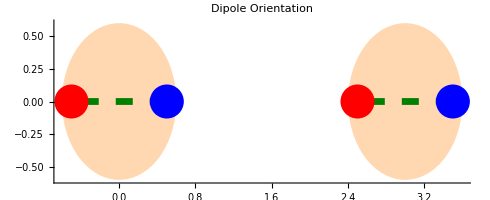

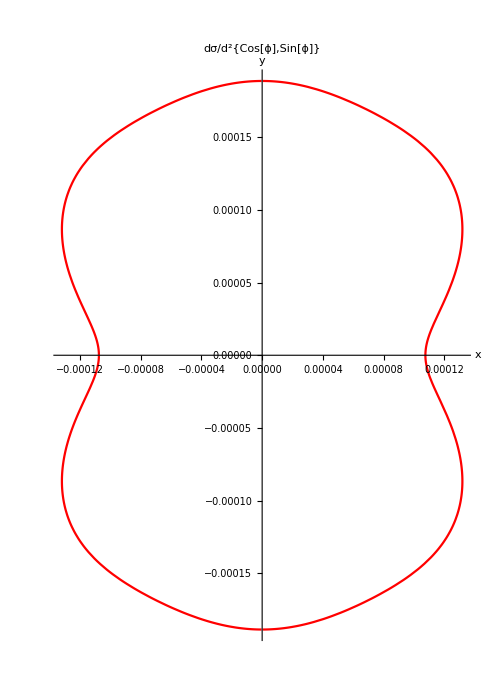

v_2=-0.114285+0. ⅈ

```mathematica
x1u={1/2,0};
x2u={-1/2,0};
x3u={1/2,0};
x4u={-1/2,0};
bu={3,0};
kT=1.0;
showdσ[bu,x1u,x2u,x3u,x4u,kT]
```

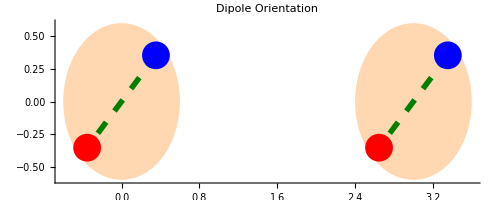

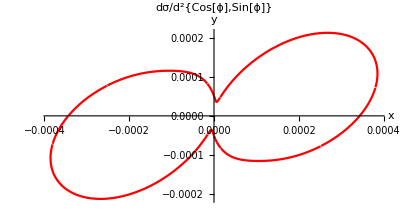

v_2=0.364805

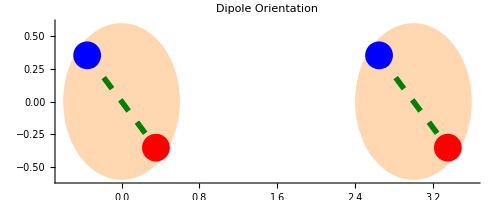

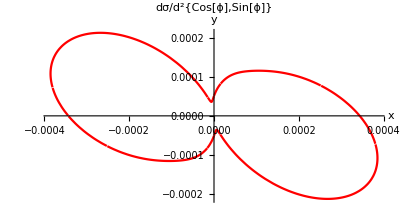

v_2=0.364805

```mathematica
x1u={1,1}/(2 Sqrt[2]);
x2u=-x1u;
x3u=x1u;
x4u=-x1u;
bu={3,0};
kT=1.0;
showdσ[bu,x1u,x2u,x3u,x4u,kT]
x1u={-1,1}/(2 Sqrt[2]);
x2u=-x1u;
x3u=x1u;
x4u=-x1u;
bu={3,0};
kT=1.0;
showdσ[bu,x1u,x2u,x3u,x4u,kT]
```

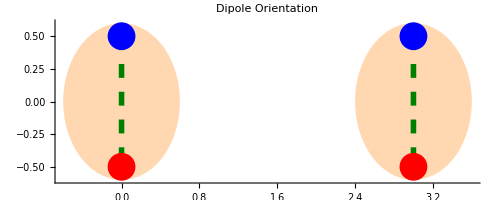

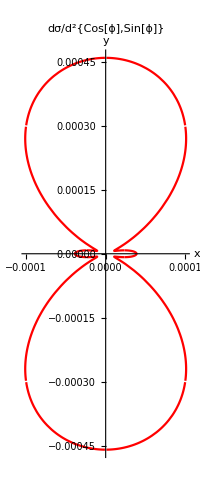

v_2=-0.669888+0. ⅈ

```mathematica
x1u={0,1/2};
x2u=-x1u;
x3u=x1u;
x4u=-x1u;
bu={3,0};
kT=1.0;
showdσ[bu,x1u,x2u,x3u,x4u,kT]
```

Therefore, we have v2 in hadron - hadron collisions.

### kT>>1/r

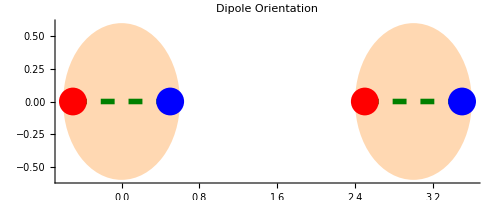

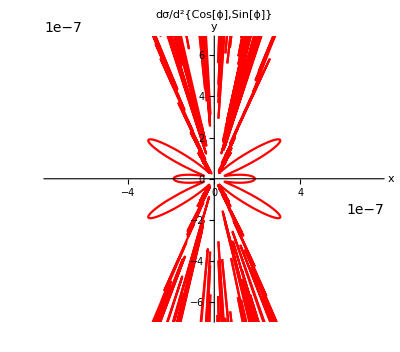

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$609 near {ϕ$609} = {1.58297}. NIntegrate obtained -0.0000256738+0. ⅈ and 1.66553×10^-6 for the integral and error estimates.

NIntegrate::levmaxord: … is a Levin function of differential order 51 which exceeds value of option "MaxOrder" -> 50. Treating … as a non-Levin function.

NIntegrate::levmaxord: (10. ⅇ^Abs[0.+20. Sin[ϕ$609]] Cos[ϕ$609] (0.-20. Sin[ϕ$609]) (CosIntegral[1/2 (0.-ⅈ Abs[0.+Times[«2»]]-20. Cos[ϕ$609])]+CosIntegral[1/2 (0.+ⅈ Abs[0.+Times[«2»]]-20. Cos[ϕ$609])]-SinhIntegral[1/2 (Abs[0.+Times[«2»]]+ⅈ (0.+Times[«2»]))]+ⅈ SinIntegral[1/2 (0.+ⅈ Abs[Plus[«2»]]+20. Cos[ϕ$609])]))/Abs[0.+20. Sin[ϕ$609]] is a Levin function of differential order 72 which exceeds value of option "MaxOrder" -> 50. Treating (10. ⅇ^Abs[0.+20. Sin[ϕ$609]] Cos[ϕ$609] (0.-20. Sin[ϕ$609]) (CosIntegral[1/2 (0.-ⅈ Abs[0.+Times[«2»]]-20. Cos[ϕ$609])]+CosIntegral[1/2 (0.+ⅈ Abs[0.+Times[«2»]]-20. Cos[ϕ$609])]-SinhIntegral[1/2 (Abs[0.+Times[«2»]]+ⅈ (0.+Times[«2»]))]+ⅈ SinIntegral[1/2 (0.+ⅈ Abs[Plus[«2»]]+20. Cos[ϕ$609])]))/Abs[0.+20. Sin[ϕ$609]] as a non-Levin function.

General::stop: Further output of NIntegrate::levmaxord will be suppressed during this calculation.

NIntegrate::errprec: Catastrophic loss of precision in the global error estimate due to insufficient WorkingPrecision or divergent integral.

v_2=-(0.0000256738+0. ⅈ)/NIntegrate[dσ[{3,0},{1/2,0},{-1/2,0},{1/2,0},{-1/2,0},{10.,ϕ$609}],{ϕ$609,0,2 π}]

```mathematica
x1u={1/2,0};
x2u={-1/2,0};
x3u={1/2,0};
x4u={-1/2,0};
bu={3,0};
kT=10.0;
showdσ[bu,x1u,x2u,x3u,x4u,kT]
```

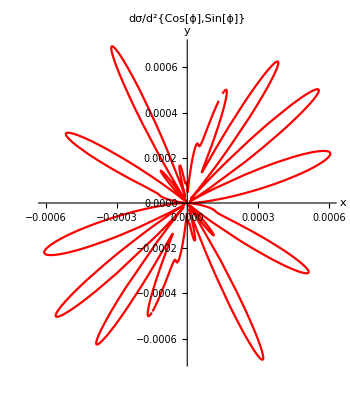

v_2=-0.0142743+0. ⅈ

-Graphics-

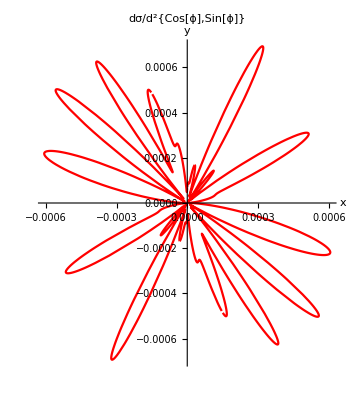

v_2=-0.0142743+0. ⅈ

```mathematica
kT=10.0;
x1u={1,1}/(2 Sqrt[2]);
x2u=-x1u;
x3u=x1u;
x4u=-x1u;
bu={3,0};
showdσ[bu,x1u,x2u,x3u,x4u,kT]
x1u={-1,1}/(2 Sqrt[2]);
x2u=-x1u;
x3u=x1u;
x4u=-x1u;
bu={3,0};
showdσ[bu,x1u,x2u,x3u,x4u,kT]
```

-Graphics-

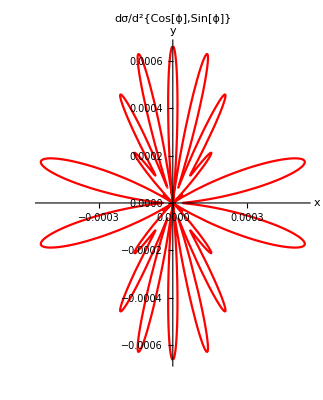

v_2=-0.0402007+0. ⅈ

```mathematica
x1u={0,1/2};
x2u=-x1u;
x3u=x1u;
x4u=-x1u;
bu={3,0};
kT=10.0;
showdσ[bu,x1u,x2u,x3u,x4u,kT]
```

Conclusion : for large k_T, the two partons can be treated as independent and the soft gluon can be taken as radiated uncoherently from the two individual partons.

### kT<<1/r

-Graphics-

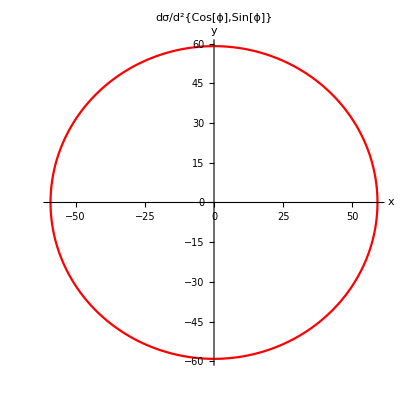

v_2=0.000347844+9.38067×10^-19 ⅈ

```mathematica
x1u={1/2,0};
x2u={-1/2,0};
x3u={1/2,0};
x4u={-1/2,0};
bu={3,0};
kT=0.1;
showdσ[bu,x1u,x2u,x3u,x4u,kT]
```

-Graphics-

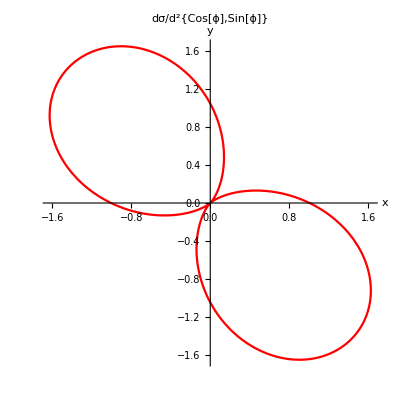

v_2=-0.0103349+8.84144×10^-19 ⅈ

-Graphics-

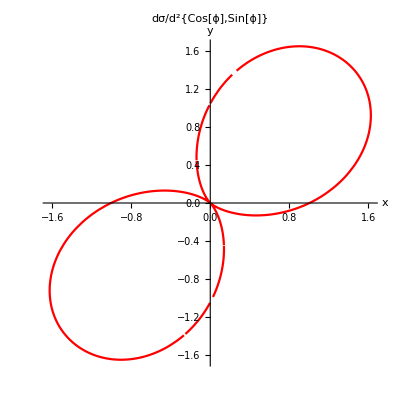

v_2=-0.0103349-2.30944×10^-19 ⅈ

```mathematica
x1u={1,1}/Sqrt[8];
x2u=-x1u;
x3u=x1u;
x4u=-x1u;
bu={3,0};
kT=0.1;
showdσ[bu,x1u,x2u,x3u,x4u,kT]
x1u={-1,1}/Sqrt[8];
x2u=-x1u;
x3u=x1u;
x4u=-x1u;
bu={3,0};
kT=0.1;
showdσ[bu,x1u,x2u,x3u,x4u,kT]
```

-Graphics-

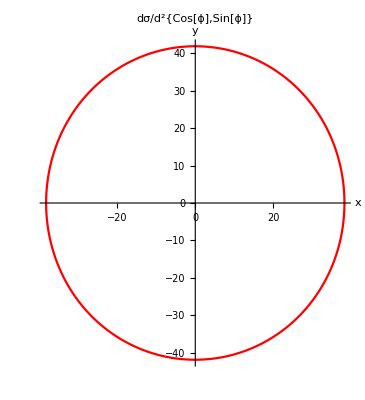

v_2=-0.0226608-1.3638×10^-18 ⅈ

```mathematica
x1u={0,1/2};
x2u=-x1u;
x3u=x1u;
x4u=-x1u;
bu={3,0};
kT=0.1;
showdσ[bu,x1u,x2u,x3u,x4u,kT]
```

Conclusion : for small k_T, radiation from the two partons can not distinguish the seperation of the dipole, hence v_2 is also negligible.